# Équation de Legendre associée

## Équation de Legendre associée

```mathematica
LegendreAs=(1-μ^2)P''[μ]-2μ P'[μ]-m^2/(1-μ^2)P[μ]+l(l+1)P[μ]==0;
```

```mathematica
DSolve[LegendreAs,P[μ],μ]//TraditionalForm
```

{{P(μ)→c_1 P_l^m(μ)+c_2 Q_l^m(μ)}}

## Les polynômes de Legendre associés de première espèce

### En coordonnées cartésiennes

```mathematica
l=3;
```

```mathematica
m=2;
```

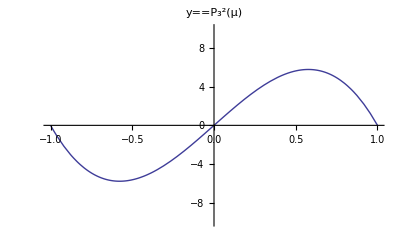

```mathematica
Plot[LegendreP[l,m,μ],{μ,-1,1},PlotRange->{{-1,1},{-10,10}},PlotLabel->Style[With[{l=l,m=m},HoldForm[y==LegendreP[l,m,μ]]],15]]
```

```mathematica
Clear[l];
```

```mathematica
Clear[m];
```

```mathematica
Grid[Table[LegendreP[l,m,μ],{l,0,3},{m,0,l}],Frame->All]
```

1 |  |  | 
μ | -√(1-μ^2) |  | 
1/2 (-1+3 μ^2) | -3 μ √(1-μ^2) | -3 (-1+μ^2) | 
1/2 (-3 μ+5 μ^3) | -3/2 √(1-μ^2) (-1+5 μ^2) | -15 μ (-1+μ^2) | -15 (1-μ^2)^(3/2)

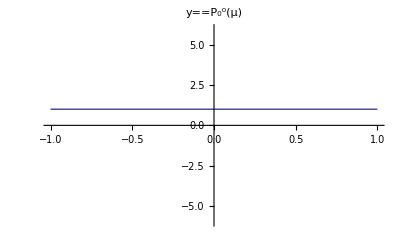
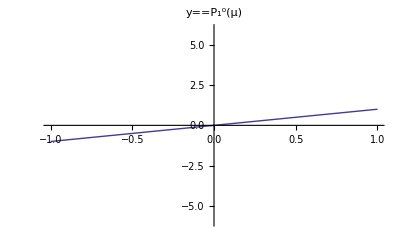
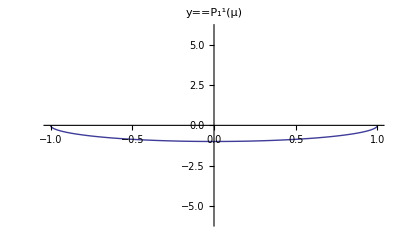
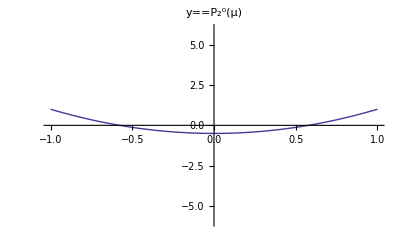
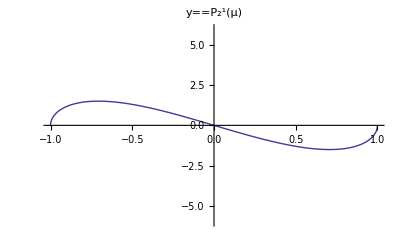
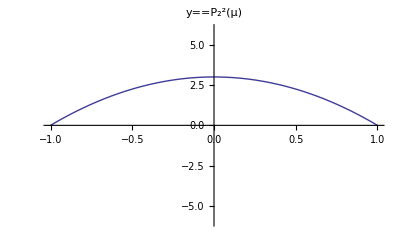
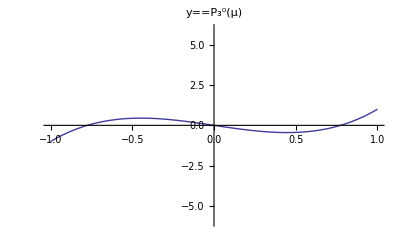
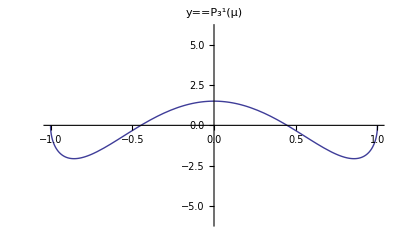
-Graphics- |  |  | 
-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Table[Plot[LegendreP[l,m,μ],{μ,-1,1},PlotRange->{{-1,1},{-6,6}},PlotLabel->Style[With[{l=l,m=m},HoldForm[y==LegendreP[l,m,μ]]],15]],{l,0,3},{m,0,l}],Spacings->{3,3},Frame->All]
```

### En coordonnées polaires

```mathematica
l=3;
```

```mathematica
m=2;
```

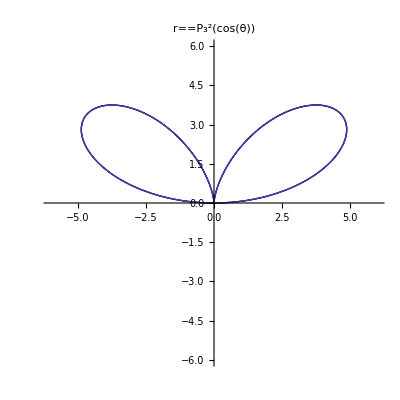

```mathematica
ParametricPlot[{Sin[θ],Cos[θ]}LegendreP[l,m,Cos[θ]],{θ,0,2π},PlotRange->6,PlotLabel->Style[With[{l=l,m=m},HoldForm[r==LegendreP[l,m,Cos[θ]]]],15]]
```

```mathematica
Clear[l];
```

```mathematica
Clear[m];
```

```mathematica
Grid[Table[LegendreP[l,m,Cos[θ]],{l,0,3},{m,0,l}],Frame->All]
```

1 |  |  | 
Cos[θ] | -√(1-Cos[θ]^2) |  | 
1/2 (-1+3 Cos[θ]^2) | -3 Cos[θ] √(1-Cos[θ]^2) | -3 (-1+Cos[θ]^2) | 
1/2 (-3 Cos[θ]+5 Cos[θ]^3) | -3/2 √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) | -15 Cos[θ] (-1+Cos[θ]^2) | -15 (1-Cos[θ]^2)^(3/2)

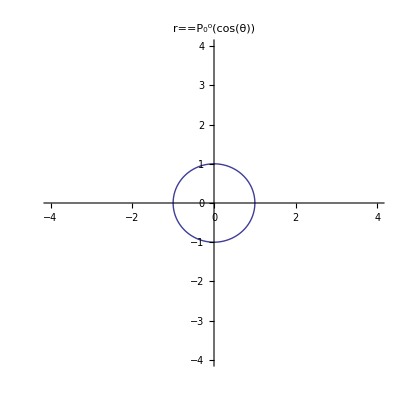
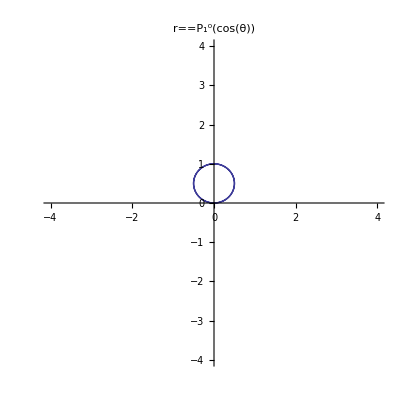
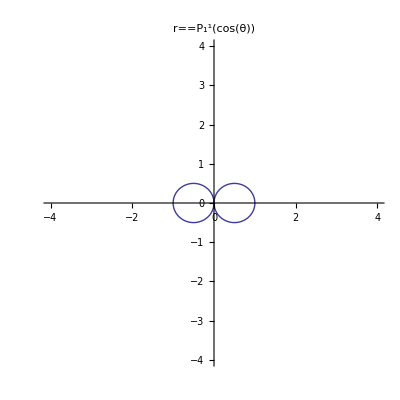
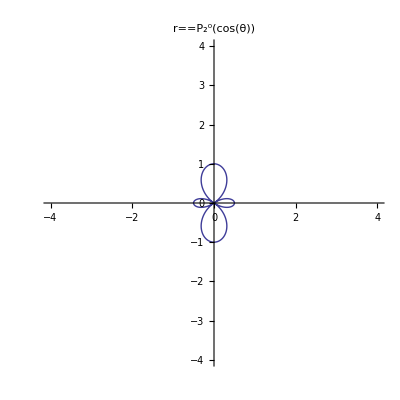
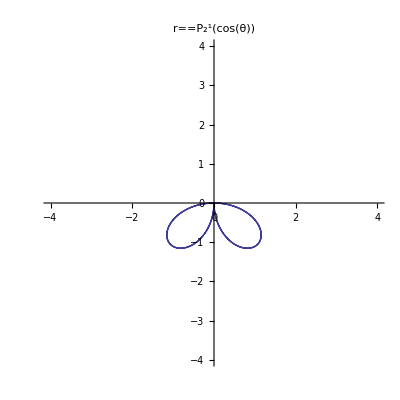
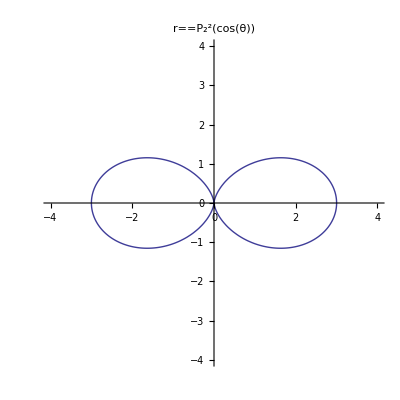
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Table[ParametricPlot[{Sin[θ],Cos[θ]}LegendreP[l,m,Cos[θ]],{θ,0,2π},PlotRange->4,PlotLabel->Style[With[{l=l,m=m},HoldForm[r==LegendreP[l,m,Cos[θ]]]],15]],{l,0,2},{m,0,l}],Spacings->{3,3},Frame->All]
```

## Les formules qui donnent les polynômes de Legendre associés

```mathematica
l=4;
```

```mathematica
m=2;
```

### Pour les exposants positif

P_l^m(μ) :

```mathematica
(-1)^m(1-μ^2)^(m/2) D[LegendreP[l,μ],{μ,m}]//Simplify
```

-15/2 (-1+μ^2) (-1+7 μ^2)

P_l^m(μ) :

```mathematica
(-1)^l((l+m)!)/((l-m)!)((1-μ^2)^(-m/2))/(2^l l!) D[(1-μ^2)^l,{μ,l-m}]//Simplify
```

-15/2 (-1+μ^2) (-1+7 μ^2)

Le code de Mathematica :

```mathematica
LegendreP[l,m,μ]//Simplify
```

-15/2 (-1+μ^2) (-1+7 μ^2)

### Pour les exposant négatif

P_l^-m(μ) :

```mathematica
(-1)^m((l-m)!)/((l+m)!)LegendreP[l,m,μ]//Simplify
```

-1/48 (-1+μ^2) (-1+7 μ^2)

P_l^-m(μ) :

```mathematica
(-1)^(l+m)((1-μ^2)^(-m/2))/(2^l l!) D[(1-μ^2)^l,{μ,l-m}]//Simplify
```

-1/48 (-1+μ^2) (-1+7 μ^2)

Le code de Mathematica :

```mathematica
LegendreP[l,-m,μ]//Simplify
```

-1/48 (-1+μ^2) (-1+7 μ^2)

```mathematica
Clear[l]
```

```mathematica
Clear[m]
```

## Parité

```mathematica
l=4;
```

```mathematica
m=3;
```

```mathematica
LegendreP[l,m,-μ]==(-1)^(l+m)LegendreP[l,m,μ]
```

True

```mathematica
Clear[l]
```

```mathematica
Clear[m]
```

## Relation d'orthonormalité

### En coordonnées cartésiennes

∫_-1^1 P_l'^m(μ) P_l'^m(μ)ⅆμ=((l+m)!)/((l-m)!)2/(2l+1)δ_ll'

```mathematica
l=3;l'=3;
```

```mathematica
m=2;
```

```mathematica
∫_-1^1 LegendreP[l,m,μ]LegendreP[l',m,μ]ⅆμ
```

240/7

```mathematica
Clear[l]
```

```mathematica
Clear[m]
```

### En coordonnées polaires

∫_0^π P_l'^m(cosθ) P_l'^m(cosθ)sinθⅆθ=((l+m)!)/((l-m)!)2/(2l+1)δ_ll'

```mathematica
l=3;l'=3;
```

```mathematica
m=2;
```

```mathematica
∫_0^π LegendreP[l,m,Cos[θ]]LegendreP[l',m,Cos[θ]]Sin[θ]ⅆθ
```

240/7

```mathematica
Clear[n]
```

```mathematica
Clear[l]
```

```mathematica
Clear[m]
```